# Vibration Characteristics of a Two Story Building

Julian Ly Davis

Often times buildings can be modeled as if the floors have independent mass supported by beams of measurable stiffness. Here we determine frequency response or transfer function of a two story house.

-Graphics-

## Problem Description

Learning Objective: Determine the transfer function of a two story (two-degree-of-freedom building) .

Given: The 2 story building has the following properties: Each support column is made of square cross-sectional 150 "mm"×150 "mm" steel, with stiffness  k_1=k_2=12E I/L^3 and modulus E=200  "GPa" and length L_1=L_2=10  "m". The floors have m_1=200,000  "kg" and m_2=300000  "kg".  Assume the columns are lightly damped, that is assume c_1=c_2=7000  "N" "s"/ "m".

Find: The transfer-functions relating the displacement of each mass to the forcing of each floor.

## Solution

### Parameters

Define the parameters:

```mathematica
Knowns1={m1->200000,m2->1.5 200000,E1->200 10^9,I1->1/12 (0.150)^4,L1->10,E2->200 10^9,I2->1/12 (0.150)^4,L2->10};
```

### Construct the Parameter Matrices

Construct the mass matrix:

```mathematica
M:=({{m1, 0}, {0, m2}})
M/.Knowns1//MatrixForm
```

(200000 | 0
0 | 300000.)

Construct the stiffness matrix:

```mathematica
K:=({{((12E1 I1)/L1^3+(12 E2 I2)/L2^3), -((12E2 I2)/L2^3)}, {-((12 E2 I2)/L2^3), ((12 E2 I2)/L2^3)}})
K/.Knowns1//MatrixForm
```

(202500. | -101250.
-101250. | 101250.)

Construct the proportional damping matrix:

```mathematica
Cdamp:=({{(2 7000+2 7000), -(2 7000)}, {-(2 7000), (2 7000)}})
```

### Compute the Transfer Functions

Now, in the Laplace domain, we can determine the transfer functions that relate the response of each floor to any input force F1 or F2:

```mathematica
eqns=s^2 M.{X1,X2}+s Cdamp.{X1,X2}+K.{X1,X2}-{F1,F2}=={0,0}/.Knowns1
```

{-F1+202500. X1+200000 s^2 X1+s (28000 X1-14000 X2)-101250. X2,-F2-101250. X1+101250. X2+300000. s^2 X2+s (-14000 X1+14000 X2)}=={0,0}

Solve the equations for X1 and X2:

```mathematica
XVF=First@Solve[eqns,{X1,X2}]//Simplify
```

{X1→(F2 (1.6875×10^-6+2.33333×10^-7 s)+F1 (1.6875×10^-6+2.33333×10^-7 s+5.×10^-6 s^2))/(0.170859+0.04725 s+1.35327 s^2+0.186667 s^3+1. s^4),X2→(F1 (0.0000122042+3.375×10^-6 s+2.33333×10^-7 s^2)+F2 (0.0000244085+6.75×10^-6 s+0.0000245738 s^2+3.33333×10^-6 s^3))/(1.23568+0.512578 s+9.83427 s^2+2.70327 s^3+7.41881 s^4+1. s^5)}

Displacement of 1st floor given forces at 1st or 2nd floor:

```mathematica
X1/.XVF
```

(F2 (1.6875×10^-6+2.33333×10^-7 s)+F1 (1.6875×10^-6+2.33333×10^-7 s+5.×10^-6 s^2))/(0.170859+0.04725 s+1.35327 s^2+0.186667 s^3+1. s^4)

Displacement of 1st floor given forces at 1st or 2nd floor:

```mathematica
X2/.XVF
```

(F1 (0.0000122042+3.375×10^-6 s+2.33333×10^-7 s^2)+F2 (0.0000244085+6.75×10^-6 s+0.0000245738 s^2+3.33333×10^-6 s^3))/(1.23568+0.512578 s+9.83427 s^2+2.70327 s^3+7.41881 s^4+1. s^5)

### Bode Plots

Display a BodePlot of X1& X2 with a unit force applied to the second floor:

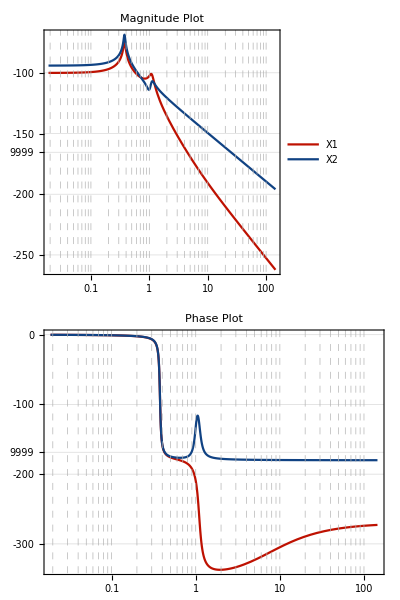

```mathematica
BodePlot[{X1,X2}/.XVF/.{{F1->0,F2->1}},]
```

Display a BodePlot of X1& X2 with either a unit force applied to the first floor only:

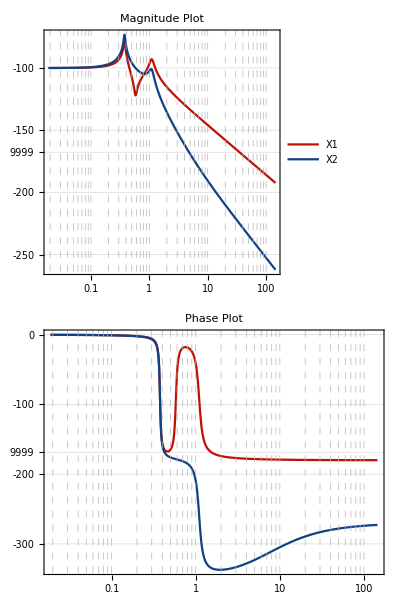

```mathematica
BodePlot[{X1,X2}/.XVF/.{F1->1,F2->0},]
```

Notice that the anti-resonance (the inverted peak in the red graph below) has appeared (between the two peaks). This is an indication that if the structure is excited at this frequency, that the first floor will displace minimally when compared with the second floor displacement.

### Manipulate the Bode Plot

An interactive BodePlot of {X1,X2} with a variable force on each floor:

```mathematica
Manipulate[BodePlot[{X1,X2}/.XVF/.{F1->F1v,F2->F2v},],
{F1v,0.0001,100},{F2v,0.0001,100},SaveDefinitions->True]
```

### Summary Questions

Now: Play with the example above to vary the magnitude of forces applied to each floor and answer the questions below.

1. At what RATIO of forces is there only ONE PEAK in each of the graphs (red and blue)? check to see that the ratio is in fact valid by trying different force values at the same ratio.

2. What happened to the phase plot?

3. What do you think this means about the directions in which each of the floors are oscillating, with respect to each other?